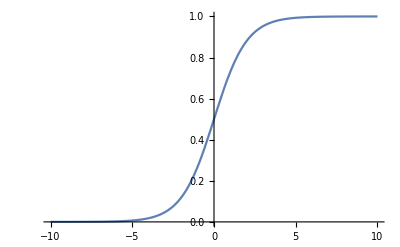

```mathematica
Plot[1/(1+Exp[-x]),{x, -10, 10}]
```

```mathematica
h[x_]:=x^2;
cost[x_,y_]:=-y Log[h[x]]-(1-y) Log[1-h[x]];
Plot3D[cost[x, y],{x, 0,1},{y,0,1}, AxesLabel->Automatic]
```

-Graphics3D-